```mathematica
Clear["Global`*"]
```

can easily get reflection parameters from here: http://refractiveindex.info/legacy/?group=GLASSES&material=F_SILICA&option=HO&wavelength=.589
this is also where I got the refractive indices. 

work in the phasor convention of e^-ikz
For each polarization component we use, eg. E_i = E_i0 e^-ikzx̂
and the ratio between the coefficients E_i0 and E_t0 is given by τ, etc....

fresnel formulas from http://my.ece.ucsb.edu/York/Bobsclass/144A/Handouts/Reflection_Refraction.pdf

# phase shift of S and P polarized field upon passing thru a glass plate at AOI θi perp vs para refers to E field pol. wrt plane of incidence. “perp” = parallel to surface note, transmission thru the glass cell doesn’t change the phase relation of S and P beams.

```mathematica
μ0=4 π 10^-7;
ϵ0=8.85 10^-12;


thickFS=4 10^-3; (*glass thickness*)
dFS = thickFS/Cos[θt]; (*distance traveled thru glass*)

thickAir=4 10^-3; (*thickness of air in cell*)
dAir = thickAir/Cos[θi]; (*distance traveled thru air*)


nAir=1;(*air*)
nFS= 1.45247; (*FS at 852 nm*)
ηFS=√(μ0/(nFS^2 ϵ0));
ηAir=√(μ0/ϵ0);

Γperp[η1_,η2_,θi_,θt_]:= (η2 Sec[θt]-η1 Sec[θi])/(η2 Sec[θt]+η1 Sec[θi]);
Γpara[η1_,η2_,θi_,θt_]:= (η2 Cos[θt]-η1 Cos[θi])/(η2 Cos[θt]+η1 Cos[θi]);


τperp[η1_,η2_,θi_,θt_]:= (2 η2 Sec[θt])/(η2 Sec[θt]+η1 Sec[θi]);
τpara[η1_,η2_,θi_,θt_]:= (2 η2 Cos[θi])/(η2 Cos[θt]+η1 Cos[θi]);

λ=852 10^-9;
k=(2π)/λ;

θi=55 π/180;
θt[θi_]:=ArcSin[(nAir Sin[θi])/nFS]; (*for air to glass interface*)
```

## phase and amplitude differences.

```mathematica
data=Reap[
Do[
(*air-glass interface*)
s1=τperp[ηAir,ηFS,θi,θt[θi]];
(*prop. thru glass*)
s2=Exp[-I nFS k dFS ];
(*glass-air interface*)
s3=τperp[ηFS,ηAir,θt[θi],θi];
(*prop. thru air*)
s4=Exp[-I nAir k dAir ];

(*to middle of cell*)
PerpAbs=Abs[s1 s2 s3 s4^(1/2)];
(*thru entire cell is just the square of this.*)



(*air-glass interface*)
s1=τpara[ηAir,ηFS,θi,θt[θi]];
(*prop. thru glass*)
s2=Exp[-I nFS k dFS ];
(*glass-air interface*)
s3=τpara[ηFS,ηAir,θt[θi],θi];
(*prop. thru air*)
s4=Exp[-I nAir k dAir ];

(*to middle of cell*)
ParaAbs=Abs[s1 s2 s3 s4^(1/2)];
(*thru entire cell is just the square of this.*)

Sow[{θi 180/π,PerpAbs/ParaAbs}];
,
{θi,0,π/2,.1}
]
][[2,1]];
```

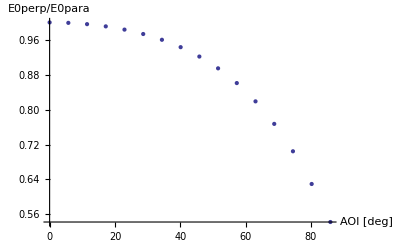

```mathematica
ListPlot[data[[;;,1;;2]],Joined->False,AxesLabel->{"AOI [deg]","E0perp/E0para"}]
```

## brewster’s angle:

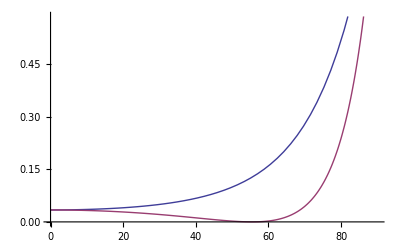

```mathematica
Plot[{Abs[Γperp[ηAir,ηFS,θi π/180,ArcSin[(nAir Sin[θi  π/180])/nFS]]]^2,Abs[Γpara[ηAir,ηFS,θi  π/180,ArcSin[(nAir Sin[θi  π/180])/nFS]]]^2},{θi,0,90}]
```

## critical angle:

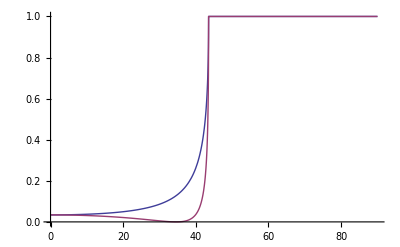

```mathematica
Plot[{Abs[Γperp[ηFS,ηAir,θi π/180,ArcSin[(nFS Sin[θi π/180])/nAir]]]^2,Abs[Γpara[ηFS,ηAir,θi π/180,ArcSin[(nFS Sin[θi π/180])/nAir]]]^2},{θi,0,90}]
```

```mathematica
Manipulate[ParametricPlot[{α Cos[θ+ϕ],Sin[θ]},{θ,0,2π-.3}],{α,.5,1},{ϕ,0,2π}]
```

## In the bloch sphere, when we have a superposition state aα + bβ, where we take α and β to be at the North and South pole, changing the relative phase between α and β means we follow a line of latitude (ie parallel to equator). Changing the relative weights means we follow a line of longitude (ie, getting closer or farther from α, β. Similarly, on the poincare sphere, if you take H, V polarized to be the North and South pole, changing the relative phase moves you along the latitudes and changing the relative weight moves you along the longitudes. determining the action of a qwp: Find the angle of the fast (slow?) axis of the qwp rel. to the H/V basis. This defines the qwp’s axis in the poincare sphere. Rotate the state by 90 degrees around the qwp axis. Eg. set the QWP axis along the H axis, locate the 45 degree LP (H+V) state. rotate it 90 degrees around the H axis to get circular. Similarly for the HWP, set the HWP axis to be H+V. Rotate the H state 180 degrees around the HWP axis to get V.

```mathematica
180 θt[55 π/180]/π
```

34.3309

^2

```mathematica
θt[55 ]
```

-0.759162